```mathematica
LP1 = 1/2({{1, Cos[2θ1], Sin[2θ1], 0}, {Cos[2θ1], Cos[2θ1]^2, Sin[2θ1]Cos[2θ1], 0}, {Sin[2θ1], Sin[2θ1]Cos[2θ1], Sin[2θ1]^2, 0}, {0, 0, 0, 0}})
LP2 = 1/2({{1, Cos[2θ2], Sin[2θ2], 0}, {Cos[2θ2], Cos[2θ2]^2, Sin[2θ2]Cos[2θ2], 0}, {Sin[2θ2], Sin[2θ2]Cos[2θ2], Sin[2θ2]^2, 0}, {0, 0, 0, 0}})
```

{{1/2,1/2 Cos[2 θ1],1/2 Sin[2 θ1],0},{1/2 Cos[2 θ1],1/2 Cos[2 θ1]^2,1/2 Cos[2 θ1] Sin[2 θ1],0},{1/2 Sin[2 θ1],1/2 Cos[2 θ1] Sin[2 θ1],1/2 Sin[2 θ1]^2,0},{0,0,0,0}}

{{1/2,1/2 Cos[2 θ2],1/2 Sin[2 θ2],0},{1/2 Cos[2 θ2],1/2 Cos[2 θ2]^2,1/2 Cos[2 θ2] Sin[2 θ2],0},{1/2 Sin[2 θ2],1/2 Cos[2 θ2] Sin[2 θ2],1/2 Sin[2 θ2]^2,0},{0,0,0,0}}

```mathematica
GQWP=({{1, 0, 0, 0}, {0, Cos[2θ]^2, Sin[2θ]Cos[2θ], Sin[2θ]}, {0, Sin[2θ]Cos[2θ], Sin[2θ]^2, -Cos[2θ]}, {0, -Sin[2θ], Cos[2θ], 0}})
```

{{1,0,0,0},{0,Cos[2 θ]^2,Cos[2 θ] Sin[2 θ],Sin[2 θ]},{0,Cos[2 θ] Sin[2 θ],Sin[2 θ]^2,-Cos[2 θ]},{0,-Sin[2 θ],Cos[2 θ],0}}

```mathematica
LP2*GQWP*LP1
```

{{1/4,0,0,0},{0,1/4 Cos[2 θ]^2 Cos[2 θ1]^2 Cos[2 θ2]^2,1/4 Cos[2 θ] Cos[2 θ1] Cos[2 θ2] Sin[2 θ] Sin[2 θ1] Sin[2 θ2],0},{0,1/4 Cos[2 θ] Cos[2 θ1] Cos[2 θ2] Sin[2 θ] Sin[2 θ1] Sin[2 θ2],1/4 Sin[2 θ]^2 Sin[2 θ1]^2 Sin[2 θ2]^2,0},{0,0,0,0}}

JONES MATRIX

16.64

ListPlot::lpn: $Failed is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ListPlot[$Failed], GraphicsBox[List[List[List[], List[], List[Directive[Opacity[1.`], RGBColor[0.368417`, 0.506779`, 0.709798`], AbsoluteThickness[1.6`]], LineBox[List[List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], Skeleton[1023]]]]]], List[Rule[DisplayFunction, Identity], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[0, 0.46`]], RuleDelayed[DisplayFunction, Identity], Rule[Frame, List[List[False, False], List[False, False]]], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLines, List[None, None]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

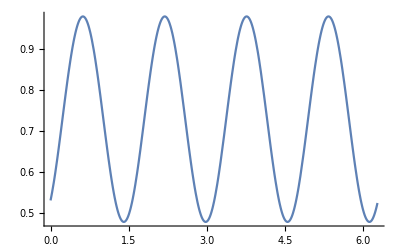
Show[ListPlot[$Failed],-Graphics-]

```mathematica
B=-10.61;
LP2=16.64
LP1=0;
θ1=π/180*(LP1);
θ2=π/180*(LP2);
β=π/180*(B);
QWP = ({{Cos[β+θ]^2+ⅈ Sin[β+θ]^2, (1-ⅈ)Sin[β+θ]Cos[β+θ]}, {(1-ⅈ)Sin[β+θ]Cos[β+θ], Sin[β+θ]^2+ⅈ Cos[β+θ]^2}});
POL=({{Cos[θ2]^2, Sin[θ2]Cos[θ2]}, {Sin[θ2]Cos[θ2], Sin[θ2]^2}});
IncVec = {Cos[θ1],Sin[θ1]};
FinalVector =POL.QWP.IncVec;
intensity = Norm[FinalVector]^2;
simulation=Plot[intensity+.02,{θ,0,2π*1198/1200}];
Show[ListPlot[tab],simulation]
```

```mathematica
tab =Import["/home/karl/data/MAT_POL2016-07-11_134540.dat","Data"];
```

Import::nffil: File not found during Import.

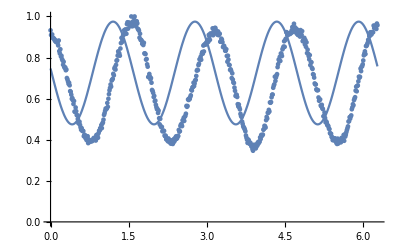

```mathematica
tab2 =Import["/home/karl/data/MAT_POL2016-07-11_143933.csv","Data"];
Show[ListPlot[tab2],simulation]
```

39.5

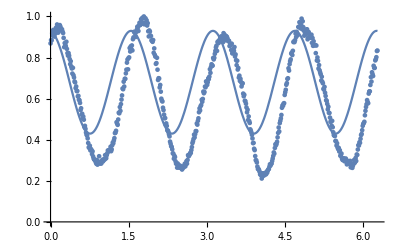

```mathematica
tab2 =Import["/home/karl/data/2016-07-11/MAT_POL2016-07-11_153325.csv","Data"];
LP1
Show[ListPlot[tab2],simulation]
```

-43.

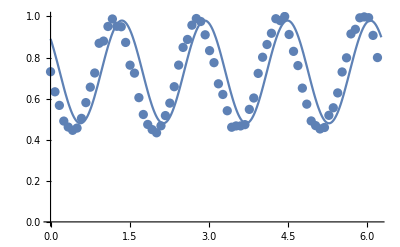

```mathematica
tab2 =Import["/home/karl/data/2016-07-11/MAT_POL2016-07-12_115944.csv","Data"];
LP1
Show[ListPlot[tab2],simulation]
```